## Final Plot of Bootstrapped EWS for Fussmann system - New colour scheme

## Import data

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/hopf_fussmann_2000"];
```

```mathematica
(* Job number *)
jobNum=6546;
```

```mathematica
(* Data directory *)
dataDir="hagrid/fussmann_ews/Jobs/job-"<>ToString[jobNum]<>"/";
```

```mathematica
(* Import parameters used *)
pars=Import[dataDir<>"pars.txt","Data"];
```

```mathematica
pars//TableForm
```

span | rw | ham_length | ham_offset | w_cutoff | sweep | block_size | bs_type | n_samples
80 | 1 | 80 | 0.5 | 1 | true | 40 | Circular | 100

```mathematica
(* EWS data *)
ewsRaw=Import[dataDir<>"ews_intervals.csv"];
```

### Bifurcation data

```mathematica
bifPtsChlor=Import["data/bifPtsChlor.mat"];
bifPtsBrach=Import["data/bifPtsBrach.mat"];
```

```mathematica
(* clear out points that go beyond max dilution rate on plot *)
bifPtsChlor=Table[DeleteCases[bifPtsChlor[[i]],{x_,_}/;x>1.5],{i,1,Length[bifPtsChlor]}];
bifPtsBrach=Table[DeleteCases[bifPtsBrach[[i]],{x_,_}/;x>1.5],{i,1,Length[bifPtsBrach]}];
```

### General figure parameters

```mathematica
(* Figure params *)
TMBcolours=ColorData[97,"ColorList"];
imgs=400;
colChlor=Darker[TMBcolours[[1]],0.15];
colBrach=Darker[TMBcolours[[4]],0.15];
```

```mathematica
aRatio=0.25; (* aspect ratio *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterSize=12;
ltb=0.005; (* line thickness for bifurcation *)
lt=0.003; (* line thickness *)
ls=9; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Bifurcation diagram

```mathematica
deltaVals=Union[ewsRaw[[2;;,1]]]
```

{0.04,0.07,0.12,0.32,0.64,0.67,0.69,0.95,1.17,1.24,1.37}

```mathematica
(* mark on approximate bifurcation points from experiment *)
expBif1a=0.32;
expBif1b=0.64;
expBif2=1.16;
expBifPts={expBif1a,expBif1b,expBif2};
```

```mathematica
(* Legend *)
legend=LineLegend[{colChlor,colBrach},{Style["Chlorella Vulgaris",ls],Style["Brachionus Calyciflorus",ls]},Spacings->{0,0.2}]
```

```mathematica
bifPlotChlor=ListLinePlot[bifPtsChlor,
PlotStyle->Table[{colChlor,Thickness[ltb]},{i,1,Length[bifPtsChlor]}],
LabelStyle->ls,
InterpolationOrder->1,
PlotRange->{{0,1.5},{0,6}*1000000},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Chlor. (10^6 cells/ml)",Style["Brach. (females/ml)",White]},{"",""}},
FrameTicks->{{Transpose[{Range[-4/40,6]*1000000,Range[0,6]}],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.4,
PlotRangeClipping->False,
PlotLegends->Placed[legend,Scaled[{0.78,0.85}]],
Epilog->{Directive[{Black}],
Line[Table[{Scaled[{0,-0.05},{deltaVals[[i]],0}],
Scaled[{0,0.05},{deltaVals[[i]],0}]},{i,1,Length[deltaVals]}]],
Directive[{Black}],Text[Style["a",labelLetterSize,Bold],labelLetterPos]}]
```

-Graphics-

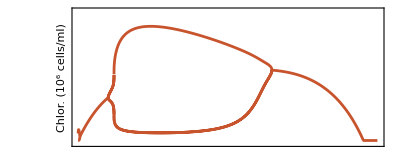

```mathematica
(* brachionus bif *)
bifPlotBrach=ListLinePlot[bifPtsBrach,
PlotRange->{{0,1.5},{-64/40,64}},
PlotStyle->Table[{colBrach,Thickness[ltb]},{i,1,Length[bifPtsBrach]}],
LabelStyle->ls,
InterpolationOrder->1,
Frame->{{False,True},{True,True}},
FrameLabel->{{Style["Chlor. (10^6 cells/ml)",White],"Brach. (females/ml)"},{"",""}},
FrameTicks->{{None,Range[0,60,10]},{None,None}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.4,
PlotRangeClipping->False]
```

## Plots of EWS against delta

```mathematica
ewsRaw[[1]]
```

{Dilution rate,Species,,Variance,Lag-1 AC,Lag-2 AC,Lag-10 AC,AIC fold,AIC hopf,AIC null,Smax}

### Variance

```mathematica
(* Index of EWS of interest *)
ewsIndex=Position[ewsRaw[[1]],"Variance"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerSeriesComp=Transpose[{lowerSeriesB[[;;,1]],Mean[{Standardize[lowerSeriesB[[;;,2]]],Standardize[lowerSeriesC[[;;,2]]]}]}];
upperSeriesComp=Transpose[{upperSeriesB[[;;,1]],Mean[{Standardize[upperSeriesB[[;;,2]]],Standardize[upperSeriesC[[;;,2]]]}]}];
meanSeriesComp=Transpose[{meanSeriesB[[;;,1]],Mean[{Standardize[meanSeriesB[[;;,2]]],Standardize[meanSeriesC[[;;,2]]]}]}];
```

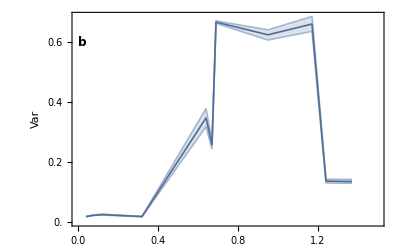

```mathematica
varPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->ls,
Filling->{{3->{1},3->{2}}},
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->{{Thickness[lt],Lighter[colChlor,0.5]},{Thickness[lt],Lighter[colChlor,0.5]},{Thickness[lt],colChlor}},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Var",""},{"",""}},
FrameTicks->{{Range[0,1,0.2],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Epilog->{Directive[{Black}],Text[Style["b",labelLetterSize,Bold],labelLetterPos]}
]
```

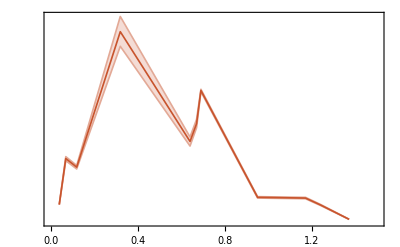

```mathematica
varPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->ls,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},All},
PlotStyle->{{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],colBrach}},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Var"},{"",""}},
FrameTicks->{{None,Range[0,50,10]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs]
```

### Variance log plot

```mathematica
varLogPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->ls,
ScalingFunctions->"Log",
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{10^(-2.5),2}},
PlotStyle->{{Lighter[colChlor,0.5],Thickness[lt]},{Lighter[colChlor,0.5],Thickness[lt]},{colChlor,Thickness[lt]}},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Variance",""},{"",""}},
FrameTicks->{{{{10^(-2),"10^-2"},{10^(-1),"10^-1"},{1,1},{10,10},{100,100}},None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Epilog->{Directive[{Black}],Text[Style["b",labelLetterSize,Bold],labelLetterPos]}
];
```

```mathematica
varLogPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->ls,
ScalingFunctions->"Log",
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{10^(-1),200}},
PlotStyle->{{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],colBrach}},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Variance"},{"",""}},
FrameTicks->{{None,{{10^(-4),"10^-4"},{10^(-2),"10^-2"},{1,1},{10,10},{100,100}}},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs];
```

### Coefficient of variation ( to be computed )

### Lag-1 AC

```mathematica
ewsIndex=Position[ewsRaw[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerSeriesComp=Transpose[{lowerSeriesB[[;;,1]],Mean[{Standardize[lowerSeriesB[[;;,2]]],Standardize[lowerSeriesC[[;;,2]]]}]}];
upperSeriesComp=Transpose[{upperSeriesB[[;;,1]],Mean[{Standardize[upperSeriesB[[;;,2]]],Standardize[upperSeriesC[[;;,2]]]}]}];
meanSeriesComp=Transpose[{meanSeriesB[[;;,1]],Mean[{Standardize[meanSeriesB[[;;,2]]],Standardize[meanSeriesC[[;;,2]]]}]}];
```

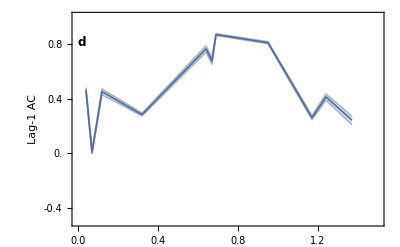

```mathematica
ac1PlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->ls,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->{{Lighter[colChlor,0.5],Thickness[lt]},{Lighter[colChlor,0.5],Thickness[lt]},{colChlor,Thickness[lt]}},
Filling->{{3->{1},3->{2}}},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Lag-1 AC",""},{"",""}},
FrameTicks->{{Range[-0.8,0.8,0.4],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Epilog->{Directive[{Black}],Text[Style["d",labelLetterSize,Bold],labelLetterPos]}]
```

```mathematica
ac1PlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->ls,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->{{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],colBrach}},
Filling->{{3->{1},3->{2}}},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Lag-1 AC"},{"",""}},
FrameTicks->{{None,Range[-0.8,0.8,0.4]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs];
```

### Smax

```mathematica
(* Index of EWS of interest *)
ewsIndex=Position[ewsRaw[[1]],"Smax"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerSeriesComp=Transpose[{lowerSeriesB[[;;,1]],Mean[{Standardize[lowerSeriesB[[;;,2]]],Standardize[lowerSeriesC[[;;,2]]]}]}];
upperSeriesComp=Transpose[{upperSeriesB[[;;,1]],Mean[{Standardize[upperSeriesB[[;;,2]]],Standardize[upperSeriesC[[;;,2]]]}]}];
meanSeriesComp=Transpose[{meanSeriesB[[;;,1]],Mean[{Standardize[meanSeriesB[[;;,2]]],Standardize[meanSeriesC[[;;,2]]]}]}];
```

```mathematica
smaxPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->ls,
Filling->{{3->{1},3->{2}}},
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->{{Lighter[colChlor,0.5],Thickness[lt]},{Lighter[colChlor,0.5],Thickness[lt]},{colChlor,Thickness[lt]}},
Frame->{{True,False},{True,True}},
FrameLabel->{{"S_max",""},{"",""}},
FrameTicks->{{Range[0,10,0.1],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Epilog->{Directive[{Black}],Text[Style["d",labelLetterSize,Bold],labelLetterPos]}
];
```

```mathematica
smaxPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->ls,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},All},
PlotStyle->{{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],colBrach}},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","S_max"},{"",""}},
FrameTicks->{{None,Range[0,10,1]//N},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}}];
```

### Smax Log Scale

```mathematica
(* Index of EWS of interest *)
ewsIndex=Position[ewsRaw[[1]],"Smax"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
smaxLogPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
ScalingFunctions->"Log",
LabelStyle->ls,
Filling->{{3->{1},3->{2}}},
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->{{Lighter[colChlor,0.5],Thickness[lt]},{Lighter[colChlor,0.5],Thickness[lt]},{colChlor,Thickness[lt]}},
Frame->{{True,False},{True,True}},
FrameLabel->{{"S_max",""},{"",""}},
FrameTicks->{{{{10^(-2),"10^-2"},{10^(-1),"10^-1"},{1,1},{10,10},{100,100}},None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Epilog->{Directive[{Black}],Text[Style["c",labelLetterSize,Bold],labelLetterPos]}
];
```

```mathematica
smaxLogPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
ScalingFunctions->"Log",
LabelStyle->ls,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},All},
PlotStyle->{{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],colBrach}},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","S_max"},{"",""}},
FrameTicks->{{None,{{10^(-2),"10^-2"},{10^(-1),"10^-1"},{1,1},{10,10},{100,100}}},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs];
```

### AIC weight fold

```mathematica
(* Index of EWS of interest *)
ewsIndex=Position[ewsRaw[[1]],"AIC fold"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerSeriesComp=Transpose[{lowerSeriesB[[;;,1]],Mean[{lowerSeriesB[[;;,2]],lowerSeriesC[[;;,2]]}]}];
upperSeriesComp=Transpose[{upperSeriesB[[;;,1]],Mean[{upperSeriesB[[;;,2]],upperSeriesC[[;;,2]]}]}];
meanSeriesComp=Transpose[{meanSeriesB[[;;,1]],Mean[{meanSeriesB[[;;,2]],meanSeriesC[[;;,2]]}]}];
```

```mathematica
aicFoldPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->ls,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->{{Lighter[colChlor,0.5],Thickness[lt]},{Lighter[colChlor,0.5],Thickness[lt]},{colChlor,Thickness[lt]}},
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_fold",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Epilog->{Directive[{Black}],Text[Style["f",labelLetterSize,Bold],labelLetterPos]}];
```

```mathematica
aicFoldPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->ls,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->{{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],colBrach}},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_fold"},{"",""}},
FrameTicks->{{None,Range[0,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs];
```

### AIC weight Hopf

```mathematica
(* Index of EWS of interest *)
ewsIndex=Position[ewsRaw[[1]],"AIC hopf"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerSeriesComp=Transpose[{lowerSeriesB[[;;,1]],Mean[{lowerSeriesB[[;;,2]],lowerSeriesC[[;;,2]]}]}];
upperSeriesComp=Transpose[{upperSeriesB[[;;,1]],Mean[{upperSeriesB[[;;,2]],upperSeriesC[[;;,2]]}]}];
meanSeriesComp=Transpose[{meanSeriesB[[;;,1]],Mean[{meanSeriesB[[;;,2]],meanSeriesC[[;;,2]]}]}];
```

```mathematica
aicHopfPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->ls,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->{{Lighter[colChlor,0.5],Thickness[lt]},{Lighter[colChlor,0.5],Thickness[lt]},{colChlor,Thickness[lt]}},
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_hopf",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Epilog->{Directive[{Black}],Text[Style["e",labelLetterSize,Bold],labelLetterPos]}];
```

```mathematica
aicHopfPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->ls,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->{{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],colBrach}},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_hopf"},{"",""}},
FrameTicks->{{None,Range[0,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs];
```

### AIC weight Null

```mathematica
(* Index of EWS of interest *)
ewsIndex=Position[ewsRaw[[1]],"AIC null"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerSeriesComp=Transpose[{lowerSeriesB[[;;,1]],Mean[{lowerSeriesB[[;;,2]],lowerSeriesC[[;;,2]]}]}];
upperSeriesComp=Transpose[{upperSeriesB[[;;,1]],Mean[{upperSeriesB[[;;,2]],upperSeriesC[[;;,2]]}]}];
meanSeriesComp=Transpose[{meanSeriesB[[;;,1]],Mean[{meanSeriesB[[;;,2]],meanSeriesC[[;;,2]]}]}];
```

```mathematica
aicNullPlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->ls,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->{{Lighter[colChlor,0.5],Thickness[lt]},{Lighter[colChlor,0.5],Thickness[lt]},{colChlor,Thickness[lt]}},
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_null",""},{"",""}},
FrameTicks->{{Range[0,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs];
```

```mathematica
aicNullPlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->ls,
InterpolationOrder->1,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->{{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],colBrach}},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_null"},{"",""}},
FrameTicks->{{None,Range[0,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs];
```

## Grid all plots together

```mathematica
lHeight1=0.148;
lHeight2=2.931;
```

### Dimensions of Figure

```mathematica
cm=72/2.54;
```

```mathematica
(* Horizontal dimensions *)
leftPad=1.6cm;
widthFig=10cm;
rightPad=1.6cm;
(* Total horizontal dimension *)
imWidth=widthFig+leftPad+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightFig=2.2cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=0.7cm;
(* Total vertical dimension *)
imHeight=5*heightFig+heightBif+5*gapVert+bottomPad+topPad;
imHeight/cm
imWidth/cm
```

18.9

13.2

### Construct figure

```mathematica
lineBase=bottomPad;
lineTop=bottomPad+5*heightFig+heightBif+5*gapVert;
```

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[aicFoldPlotBrach,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{bottomPad,0}}],{0,0},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig+bottomPad}],
Inset[Show[aicFoldPlotChlor,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{bottomPad,0}}],{0,0},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig+bottomPad}],
(* 2nd row *)
Inset[Show[aicHopfPlotBrach,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,0}}],{0,bottomPad+heightFig+gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig}],
Inset[Show[aicHopfPlotChlor,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,0}}],{0,bottomPad+heightFig+gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig}],
(* 3rd row *)
Inset[Show[ac1PlotBrach,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,0}}],{0,bottomPad+2*heightFig+2*gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig}],
Inset[Show[ac1PlotChlor,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,0}}],{0,bottomPad+2*heightFig+2*gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig}],
(* 4th row *)
Inset[Show[smaxLogPlotChlor,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,0}}],{0,bottomPad+3*heightFig+3*gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig}],
Inset[Show[smaxLogPlotBrach,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,0}}],{0,bottomPad+3*heightFig+3*gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig}],
(* 5th row  *)
Inset[Show[varLogPlotChlor,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,0}}],{0,bottomPad+4*heightFig+4*gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig}],
Inset[Show[varLogPlotBrach,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,0}}],{0,bottomPad+4*heightFig+4*gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig}],
(* 6th (top) row  *)
Inset[Show[bifPlotChlor,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,topPad}}],{0,bottomPad+5*heightFig+5*gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightBif+topPad}],
Inset[Show[bifPlotBrach,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,topPad}}],{0,bottomPad+5*heightFig+5*gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightBif+topPad}],
(* Grey coloumns and labels *)
Opacity[0.1],Directive[Darker[Black,0.6]],Rectangle[{3.8cm,lineBase},{(3.8+2.1)cm,lineTop}],
Opacity[0.1],Directive[Darker[Black,0.6]],Rectangle[{(9.4+0.05)cm,lineBase},{(9.4-0.05)cm,lineTop}],
Opacity[1],Text[Style["H1",Black,12],{4.9cm,lineTop+0.3cm}],Text[Style["H2",Black,12],{9.4cm,lineTop+0.3cm}]
},
ImageSize->{imWidth,imHeight}
];
```

### Export Figure

```mathematica
plotGrid
```

-Graphics-

```mathematica
Export["figures/finals/fussmann_ews.png",plotGrid,ImageResolution->300];
```